#### 3.1 Gompertz Equation Coupled with Logistic Equation

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;α=2;β=2;u=3;
```

Gompertz Coupled with Logistic when α = β

```mathematica
p3[t_]:=(q0*k)^{-Exp[-α*t]}*((q0*k)/(q0+(k-q0)*Exp[-α*t]))*(k)^{Exp[-α*t]}*(q0*Exp[α*t]+(k-q0))^{(-Exp[-α*t]*(k-q0))/(q0)}*(k)^{(Exp[-α*t]*(k-q0))/(q0)}*(p0)^{Exp[-α*t]}
```

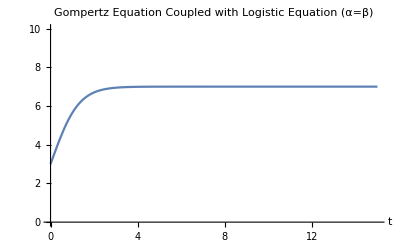

```mathematica
Plot[p3[t],{t,0,15},PlotRange->{0,10},PlotLabel->"Gompertz Equation Coupled with Logistic Equation (α=β)",AxesLabel->Automatic]
```

Gompertz Coupled with Logistic when α ≠ β

```mathematica
Quit[]
```

```mathematica
sol = DSolve[{p'[t]==-α*p[t]*Log[p[t]/((q0*k)/(q0+(k-q0)*Exp[-β*t]))],p[0]==p0},p[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→(ⅇ^(t β-(β Hypergeometric2F1[1,α/β,1+α/β,-(ⅇ^(t β) q0)/(k-q0)])/α-(ⅇ^(-t α) k (-β Hypergeometric2F1[1,α/β,1+α/β,-q0/(k-q0)]-α Log[p0/q0]))/((k-q0) α)+(ⅇ^(-t α) q0 (-β Hypergeometric2F1[1,α/β,1+α/β,-q0/(k-q0)]-α Log[p0/q0]))/((k-q0) α)) k q0)/(k-q0+ⅇ^(t β) q0)}}

```mathematica
sol1 = Simplify[sol]
```

{{p[t]→(ⅇ^((β (t α+ⅇ^(-t α) Hypergeometric2F1[1,α/β,(α+β)/β,-q0/(k-q0)]-Hypergeometric2F1[1,α/β,(α+β)/β,-(ⅇ^(t β) q0)/(k-q0)]))/α) k (p0/q0)^(ⅇ^(-t α)) q0)/(k+(-1+ⅇ^(t β)) q0)}}

```mathematica
q0=5;p0=3;k=9;α=2;β=8;
```

```mathematica
p31[t_]:=Evaluate[p[t]/.sol1]
```

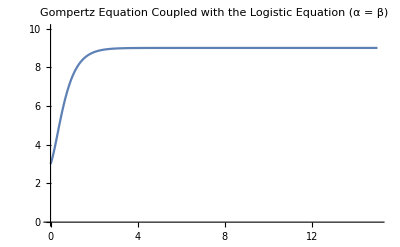

```mathematica
Plot[p31[t],{t,0,15},PlotRange->{0,10},PlotLabel->"Gompertz Equation Coupled with the Logistic Equation (α = β)"]
```